```mathematica
M={7.71,
5.76,
4.81,
4.52,
4.41,
4.25,
4.41,
4.53,
4.67,
4.75}/3+0.7
```

{3.27,2.62,2.30333,2.20667,2.17,2.11667,2.17,2.21,2.25667,2.28333}

```mathematica
Fit[M,{1,x,x^2,x^3},x]
```

3.97456-0.881028 x+0.131729 x^2-0.00608197 x^3

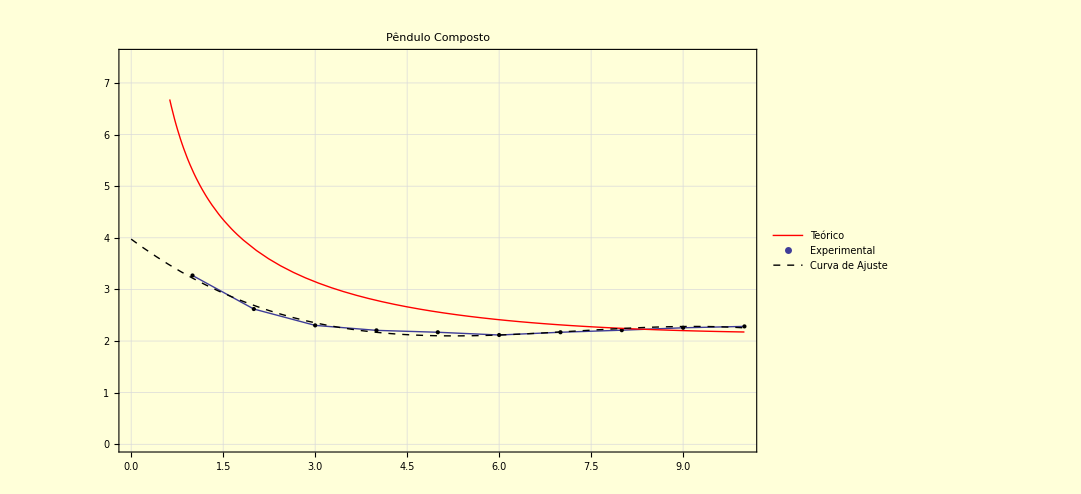

```mathematica
Show[{ListPlot[M,PlotRange->{0,7.5},Mesh->{Range[0,10,1]},MeshStyle->PointSize[Medium],Joined->True,ImageSize->800,GridLines->Automatic, PlotStyle->Thick,GridLinesStyle->Directive[Black,Dashed],Frame->True, Background->LightYellow,PlotLegends->{"Experimental"},PlotLabel->Style["Pêndulo Composto",25]],
Plot[2π Sqrt[(1/3+(0.048x)^2)/(9.8(0.048x))],{x,0,10},PlotStyle->{Red,Thick},PlotLegends->{"Teórico"}],
Plot[3.974555555555549-0.8810275835275801 x+0.13172882672882608 x^2-0.006081973581973552 x^3,{x,0,10},PlotStyle->{Black,Dashed,Thick},PlotLegends->{"Curva de Ajuste"}]

}]
```